```mathematica
Manipulate[Plot[{(1100-q)/100*a,(q+100)/200*(1-a), 1.8},{q,0, 1100},PlotLegends->{"Demand", "Supply", "Price control", "Monopsony", "Monopoly"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, Epilog->{Blue,PointSize@Large,Point[{{(100 (-1+23 a))/(1+a),-(12 (-1+a) a)/(1+a)},{0,0}}]}, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic, {Thick, Dotted}, Dashed,Dashed},GridLines->{{{500,Red}},None}, GridLinesStyle->Directive[Gray, Dotted, Thick]],{a,0.5,1}]
```

```mathematica
q== 30-p
p*q-1/2 q^2== (30-q)*q-1/2 q^2
```

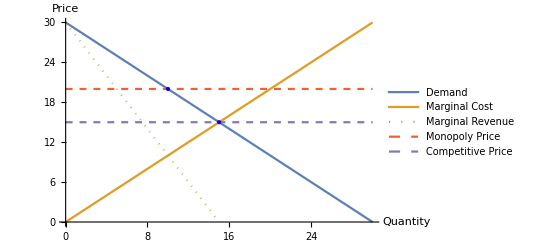

```mathematica
Plot[{30-q,q,30-2q, 20,15},{q,0, 30},PlotLegends->{"Demand", "Marginal Cost", "Marginal Revenue", "Monopoly Price", "Competitive Price"}, PlotRange->{0, Automatic}, FillingStyle->Automatic, Epilog->{Blue,PointSize@Large,Point[{{15,15},{10,20}}]}, AxesLabel->{"Quantity","Price"}, PlotStyle->{Automatic, Automatic, {Thick, Dotted}, Dashed,Dashed},GridLines->{{{500,Red}},None}, GridLinesStyle->Directive[Gray, Dotted, Thick]]
```

```mathematica
D[(30-q)*q-1/2 q^2,q]
```

30-3 q